## Generate(SAT) 10-Hexagon cluster

#### Quick depict hexagons function

```mathematica
quickDepictHexagons[code_,opt:OptionsPattern[
Join[Options[Graphics],{Opacity->1,"Arrow"->True,"Points"->True,"ArrowSize"->.05}]]
]:=Graphics[
{
Opacity[OptionValue[Opacity]],
EdgeForm[Black],
Replace[
code,
{pos_,color_,dir_}:>
With[
{vs=RotateLeft[CirclePoints[pos,{2,Pi},6],dir/2]},
{
color,
Polygon[vs],
If[TrueQ[OptionValue["Points"]],
{Black,
Disk[Mean[{Mean[vs[[{5,6}]]],pos}],.2]}
]
,
If[TrueQ[OptionValue["Arrow"]],
{Gray,
Arrowheads[OptionValue["ArrowSize"]],
Arrow[
{Mean[{Mean[vs[[{2,3}]]],pos}],
Mean[{Mean[vs[[{5,6}]]],pos}]
}
]}]
}]
,{1}
]
},Sequence@@FilterRules[{opt},Options[Graphics]]
]
```

#### Information needed (color and configurations)

```mathematica
colorToIndex=<|RGBColor[0.6, 0.6727272727272726, 1.]->1,RGBColor[0.6, 0.890909090909091, 1.]->2,RGBColor[0.6, 1., 0.6727272727272726]->3,RGBColor[0.6, 1., 0.8909090909090909]->4,RGBColor[0.7454545454545454, 0.6, 1.]->5,RGBColor[0.7454545454545455, 1., 0.6]->6,RGBColor[0.9636363636363636, 0.6, 1.]->7,RGBColor[0.9636363636363636, 1., 0.6]->8,RGBColor[1., 0.6, 0.8181818181818183]->9,RGBColor[1., 0.8181818181818181, 0.6]->10|>;
indexToColor=<|1->RGBColor[0.6, 0.6727272727272726, 1.],2->RGBColor[0.6, 0.890909090909091, 1.],3->RGBColor[0.6, 1., 0.6727272727272726],4->RGBColor[0.6, 1., 0.8909090909090909],5->RGBColor[0.7454545454545454, 0.6, 1.],6->RGBColor[0.7454545454545455, 1., 0.6],7->RGBColor[0.9636363636363636, 0.6, 1.],8->RGBColor[0.9636363636363636, 1., 0.6],9->RGBColor[1., 0.6, 0.8181818181818183],10->RGBColor[1., 0.8181818181818181, 0.6]|>;
```

```mathematica
confs=;
```

#### Hexagons location functions

```mathematica
getNeighborCoordinates[pos_List]:=+Threaded[pos]
```

```mathematica
buildHexagon[pos_,dir_]:=RotateLeft[CirclePoints[pos,{2,Pi},6],dir/2];
```

#### Main generate Hat hexagons

```mathematica
generateHatHexagons[init_Association,size_Integer,OptionsPattern[{"Count"->All,"Orientated"->True}]]:=generateHatHexagons[init,size,Range[10],"Count"->OptionValue["Count"],"Orientated"->OptionValue["Orientated"]]
```

```mathematica
generateHatHexagons[init_Association,size_Integer,patterns_List,OptionsPattern[{"Count"->All,"Orientated"->True}]]:=Module[{
neighborConstraint,
centerPoints,hexagonsCenterGraph,
vars,v,
initLogic,uniqueLogic,neighborLogic,
res
},
neighborConstraint=GroupBy[First->Last][MapThread[Rule,{confs[[All,1,2]],confs[[All,2,All,1]]}]/.colorToIndex];

centerPoints=Union@@NestList[Union@@(getNeighborCoordinates/@#)&,{{0,0}},size];
hexagonsCenterGraph=Function[pt,DirectedEdge[pt,#]&/@Cases[centerPoints,Alternatives@@getNeighborCoordinates[pt]]]/@centerPoints;

vars=Association[MapIndexed[#1->Function[{ind},v[First[#2],ind]]/@patterns&,VertexList[Flatten[hexagonsCenterGraph]]]];

initLogic=And@@KeyValueMap[
Function[
{position,color},
And@@(If[color==#[[2]],Identity[#],Not[#]]&/@vars[position])
],
init
];

uniqueLogic=Apply[And,
Or@@(And[#[[1]],Sequence@@(Not/@#[[2;;]])]&/@(Function[n,RotateLeft[#,n]]/@Range[0,9]&[#]))&/@Values[Flatten/@vars]];

neighborLogic=Apply[And,
Function[vertex,
Or@@(
Function[v,
Or@@(And[v,##]&@@MapThread[
Function[{pos,color},And@@(If[#[[2]]==color,Identity[#],Not[#]]&/@vars[pos])],
{
SortBy[First@Position[getNeighborCoordinates[vertex],#]&][
Cases[
IncidenceList[Flatten[hexagonsCenterGraph],vertex],
DirectedEdge[vertex,u_]:>u]
],
#
}
]&/@neighborConstraint[v[[2]]]
)
]/@vars[vertex]
)
]/@Select[VertexList[Flatten[hexagonsCenterGraph]],VertexOutDegree[Flatten[hexagonsCenterGraph],#]==6&]
];

(*get true/false table*)
res=Select[
MapThread[Rule,{#,Flatten[Values[vars]]}]
,TrueQ[#[[1]]]&
]&/@SatisfiabilityInstances[
If[OptionValue["Count"]===All||OptionValue["Count"]>=2,Simplify,Identity][And[neighborLogic,initLogic,uniqueLogic]],
Flatten[Values[vars]],OptionValue["Count"],Method -> "SAT"];

(*generate raw code*)
res=MapThread[{#1,indexToColor[#2],0}&,{Keys[vars],SortBy[First@*Last][#][[All,2,2]]}]&/@res;
If[!TrueQ[OptionValue["Orientated"]],Return[res]];
(*get orientation*)
Function[rawCode,
Tuples[
With[{
posToColor=Association[#1->#2&@@@rawCode],
configurationToDir=Association[MapThread[Rule[#2,#1]&,{confs[[All,1,{2,3}]],confs[[All,2,All,1]]}]/.colorToIndex]
}
,
Function[v,
With[{dirs=Union[Values[KeySelect[configurationToDir,MatchQ[#,v[[3]]]&]][[All,2]]]},
Append[v[[;;2]],#]&/@dirs
]
]/@KeyValueMap[{#1,#2,(Lookup[posToColor,getNeighborCoordinates[#1],_]/.colorToIndex)}&,posToColor]
]
]
]/@res
]
```

## Grow Hexagons

### Graph functions

```mathematica
depthNode[n_Integer][g_Graph]:=Select[VertexList[g],GraphDistance[g,First[VertexList[g]],#]==n&];
```

```mathematica
leaves[g_Graph]:=Select[VertexList[g],VertexOutDegree[g,#]==0&]
```

### Configuration Group

```mathematica
configurationGroups=;
```

### Get hexagon neighbors

```mathematica
getHexagonsNeighbors[code_List]:=With[{
posToHex=Association[#1->{#2,#3}&@@@code]
},
Association@KeyValueMap[
{#1,Sequence@@#2}->Lookup[posToHex,getNeighborCoordinates[#1],_]&,
posToHex
]
]
```

### Main function

```mathematica
growHatHexgons[code_]:=Module[{
boundaryHexagons=Select[getHexagonsNeighbors[code],MemberQ[Verbatim[Blank[]]]]
,candidates
},
candidates=Association@KeyValueMap[
Function[{centralHex,neighborHex},
centralHex->
(
MapThread[Prepend[#2,#1]&,{getNeighborCoordinates[centralHex[[1]]],#}]&/@Cases[
RotateRight[{#1,Mod[#2+centralHex[[3]],12]}&@@@#,centralHex[[3]]/2]&/@configurationGroups[centralHex[[2]]]
,
neighborHex
]
)
],
boundaryHexagons
];
candidates=GroupBy[candidates,Length];

If[
KeyExistsQ[candidates,0],
(*Print["Invalid Configurations:",candidates[0]];*)Return[{}]
];
If[
KeyExistsQ[candidates,1],

(*forced exists*)
With[{res=Union[code,Sequence@@(First/@candidates[1])]},
With[{conflict=Cases[Counts[res[[All,1]]],_?(#>=2&)]},
If[
Length[conflict]>0,
(*Print["conflict position:",Keys[conflict]];*)Return[{}],
{res}
]
]
],

(*branch*)
Union[code,#]&/@First[candidates[Min[Keys[candidates]]]]
]
]
```

## Topological Functions

### Function topGraphFromHexagonTiling Definition:

```mathematica
topGraphFromHexagonTiling[codes_]:=Module[
{
	verticesInf=<||>,
	edgesInf={},
	coordinatesToIndex=<||>,
	cnt=0(*vertex counter*)
},
	Scan[
	Function[
		code,
		With[
			{vs=buildHexagon@@code[[{1,3}]]},
			
			(*Index vertices*)
			MapIndexed[
				If[!KeyExistsQ[coordinatesToIndex,#1],
					AssociateTo[coordinatesToIndex,#1->(++cnt)]
				]&,
			vs];
			
			(*Add edges*)
			AppendTo[edgesInf,
				UndirectedEdge[
					coordinatesToIndex[vs[[#1]]],
					coordinatesToIndex[vs[[#2]]],
					{#1,#2,code[[{2,3}]]}]
				]&@@@Partition[Range[Length[vs]],2,1,1];
			
			(*Add vertex configuration information*)
			MapIndexed[
				If[
					KeyExistsQ[verticesInf,coordinatesToIndex[#1]],
					AppendTo[verticesInf[coordinatesToIndex[#1]],First[#2]->code[[{2,3}]]],
					AssociateTo[verticesInf,coordinatesToIndex[#1]->{First[#2]->code[[{2,3}]]}]
				]&,
			vs
			]
		]
	],
		codes
	];
	<|
		"vertex"->verticesInf,
		"edge"->edgesInf,
		"coordinates"->coordinatesToIndex
	|>
]
```

### Function updateVertexCoordinates Definition

```mathematica
updateVertexCoordinates[tileVertices_Association][edges_List]:=Module[{
	(*choose an oringal point arbitrarily*)
	IndexToCoordinates=<|1->{0,0}|>,
	(*create a queue for breadth first search to update vertex coordinates*)
	q=CreateDataStructure["Queue"]
},
	q["Push",1];
	While[!q["EmptyQ"],

		Block[{u=q["Pop"],vs},

		vs=IncidenceList[edges,u]/.{
			UndirectedEdge[u,v_,dir_]:>Rule[dir,v],
			UndirectedEdge[v_,u,dirInv_] :> Rule[dirInv[[{2,1,3}]],v]
			};

		Scan[
			If[
				(*if the vertex coordinates has not been calculated*)
				!KeyExistsQ[IndexToCoordinates, #[[2]]],
			
				(*update the coordinates*)
				AssociateTo[
					IndexToCoordinates,
						#[[2]]->Plus[
							IndexToCoordinates[u],
								Subtract @@ ( Part[
								tileVertices[#[[1,3,1]]],
								#[[1,{2,1}]]
							]) . Transpose[RotationMatrix[#[[1,3,2]] Pi/6]]
					]
				];
				(*push a new vertex*)
				q["Push",#[[2]]];
		Sow[{u->#[[2]]}]
			]&,
				vs
			]
		]
	];
	IndexToCoordinates
]
```

### depictTile Function

```mathematica
Options[depictTile]={"ShowPoints" -> True, "ChooseColor" -> Lighter@Blue, "PointSize"->.3, "EdgeForm" -> Black}
depictTile[tile_Association, opt:OptionsPattern[]] := Graphics[{
	EdgeForm[OptionValue["EdgeForm"]], OptionValue["ChooseColor"], Polygon[tile["boundary"]],
	If[
	TrueQ[OptionValue["ShowPoints"]],
	Sequence@@{
		ColorNegate[OptionValue["ChooseColor"]],
		Disk[tile["vertices"], OptionValue["PointSize"]]
		},
		Nothing]
}];
```

{ShowPoints→True,ChooseColor→RGBColor[Rational[1, 3], Rational[1, 3], 1],PointSize→0.3,EdgeForm→GrayLevel[0]}

### locateTile Function

```mathematica
locateTile[tile_Association][pos_List,dir_Integer,pt_Integer]:=With[{
	transformFunction=TranslationTransform[pos]@*RotationTransform[dir*Pi/6]@*TranslationTransform[-tile["vertices"][[pt]]]
},
	transformFunction/@tile
]
```

## Combinatorial Equivalent Tiling

### Generate a sample code from HatHexagonWangSolver

```mathematica
init=<|{0,0}->1|>;
```

```mathematica
Iconize[generateHatHexagons[init,10,"Count"->1][[1,1]]]//Timing
```

```mathematica
code=;
```

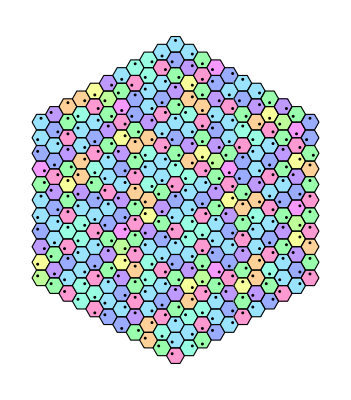

```mathematica
quickDepictHexagons[code,"Arrow"->False]
```

### Important tiles information

```mathematica
hexagonTile=;
hexagonPattern=#["vertices"]&/@hexagonTile;
```

```mathematica
hatTile=;
hatPattern=#["vertices"]&/@hatTile;
```

```mathematica
clusterTile=;
clusterPattern=#["vertices"]&/@clusterTile;
```

```mathematica
Grid[KeyValueMap[depictTile[#2,"ChooseColor"->#1,"PointSize"->.2]&,#]//Partition[#,5]&]&/@{hexagonTile,hatTile,clusterTile}//Column[#,Frame->All]&
```

-Graphics-
-Graphics-
-Graphics-

### Build topological graph

```mathematica
g=topGraphFromHexagonTiling[code];
```

```mathematica
Keys[g]
```

{vertex,edge,coordinates}

```mathematica
{
Labeled[Graph[g["edge"]],"Topological Graph"],
Labeled[Graph[g["edge"],VertexCoordinates->(KeyValueMap[Rule[#2,#1]&,g["coordinates"]]),ImageSize->200],"Graph with Coordinates Set"]
}
```

{-Graphics-Topological Graph,-Graphics-Graph with Coordinates Set}

#### Reset coordinates with different set of tiles

```mathematica
newCoordinates=updateVertexCoordinates[#][g["edge"]]&/@{hexagonPattern,hatPattern,clusterPattern};
```

```mathematica
MapThread[
Labeled[Graph[g["edge"],VertexCoordinates->#2,ImageSize->250],#1]&
,{
{"hexagon","hat","cluster"},
newCoordinates
}
]//List//Grid
```

-Graphics-hexagon | -Graphics-hat | -Graphics-cluster

### Replace with tiles

```mathematica
newCodes=Cases[
		g["edge"],
		UndirectedEdge[u_,v_,{1,p2_,code_List}]:>{newCoordinates[[#]][u],code[[1]],code[[2]],1}
	]&/@{1,2,3};
```

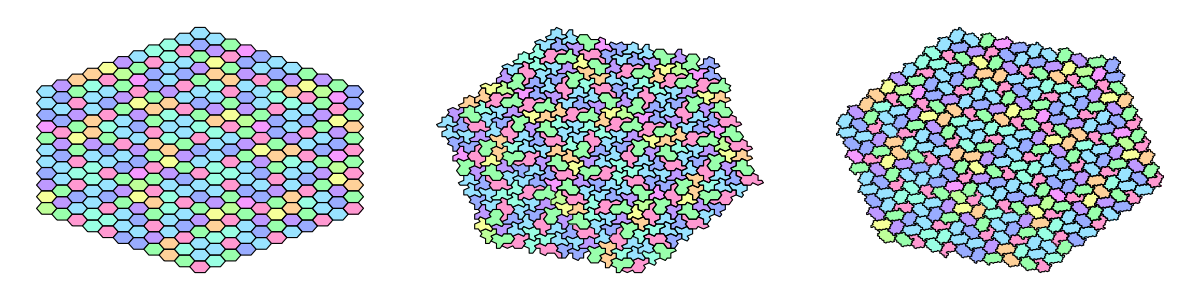

```mathematica
MapThread[
Function[{tileSet,position},
Show[Apply[
depictTile[locateTile[tileSet[#2]][#1,#3,#4],"ChooseColor"->#2,"ShowPoints"->False]&
,position
,{1}],ImageSize->330]
],
{
{hexagonTile,hatTile,clusterTile},
newCodes
}
]//List//Grid
```